```mathematica
<<Combinatorica`
<<GraphUtilities`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

MinimumVertexColoring::shdw: Symbol "MinimumVertexColoring" appears in multiple contexts {"Combinatorica`", "Global`"}; definitions in context "Combinatorica`" may shadow or be shadowed by other definitions.

ToCombinatoricaGraph::shdw: Symbol "ToCombinatoricaGraph" appears in multiple contexts {"GraphUtilities`", "Global`"}; definitions in context "GraphUtilities`" may shadow or be shadowed by other definitions.

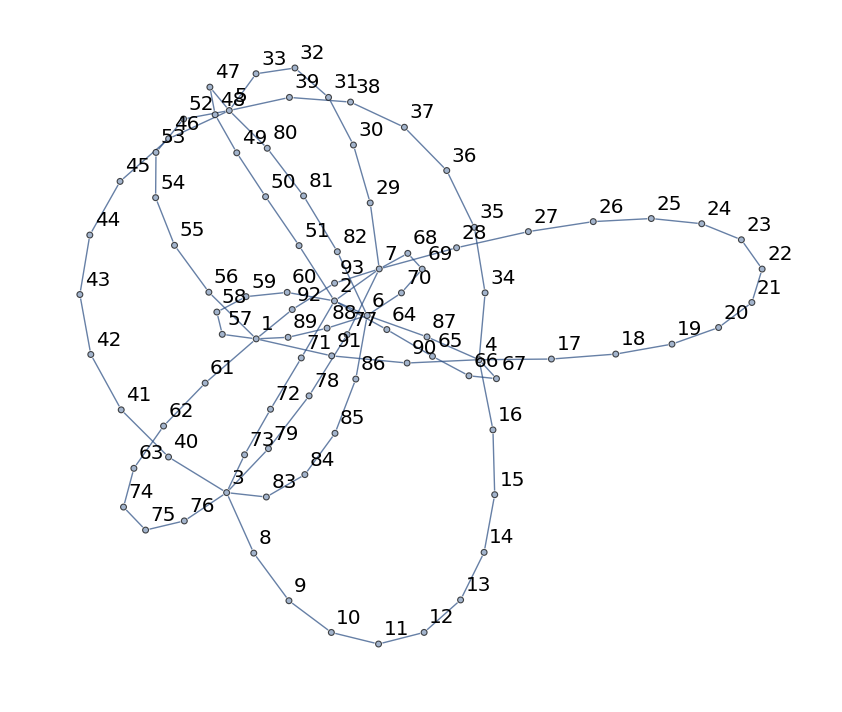

{1,2,2,2,2,2,2,2,1,1,1,1,1,2,1,1,1,1,1,2,2,2,1,2,2,2,1,2,1,1,2,1,2,1,3,1,2,1,2,3,3,2,1,2,1,2,2,1,2,3,2,1,2,1,2,1,2,3,2,1,2,1,2,3,2,1,2,2,3,1,2,1,2,3,1,2,1,2,1,2,1,2,1,2,3,1,2,1,2,1,2,1,2}

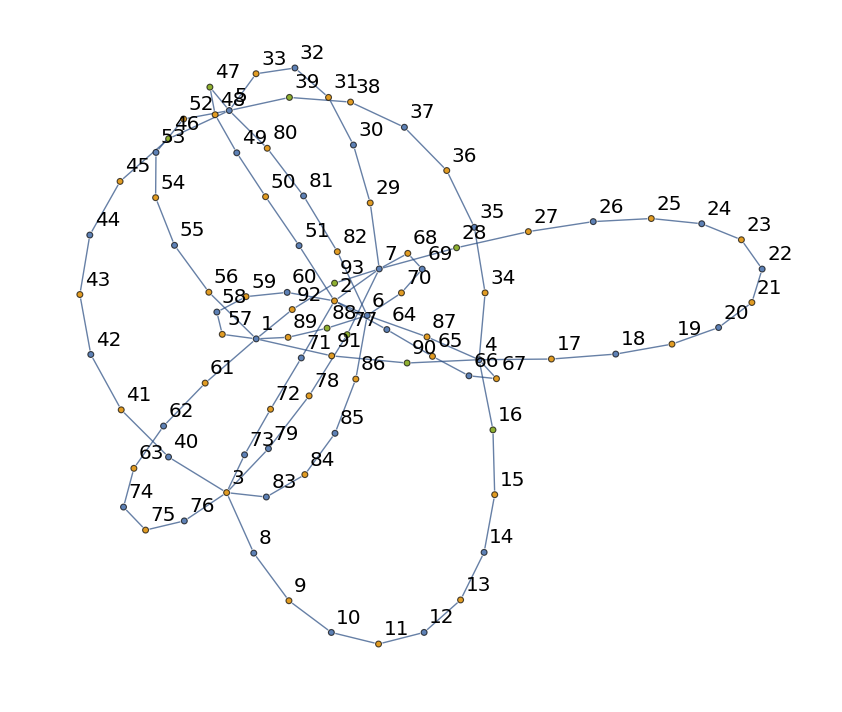

3

{1,57,61,91,56,89,92,2,71,64,51,6,7,3,8,40,83,79,4,34,87,17,5,80,33,70,58,59,60,62,63,74,75,76,90,55,54,53,52,88,93,72,73,65,66,67,50,49,48,47,9,10,11,12,13,14,15,16,41,42,43,44,45,46,84,85,86,78,77,35,36,37,38,39,18,19,20,21,22,23,24,25,26,27,28,81,82,32,31,30,29,69,68}

```mathematica
g=System`Graph[{1<->57,1<->61,1<->91,1<->56,1<->89,1<->92,2<->71,2<->64,2<->51,2<->6,2<->7,3<->8,3<->40,3<->83,3<->79,4<->34,4<->87,4<->17,5<->80,5<->33,6<->70,57<->58,58<->59,59<->60,60<->2,61<->62,62<->63,63<->74,74<->75,75<->76,76<->3,91<->90,90<->4,56<->55,55<->54,54<->53,53<->52,52<->5,89<->88,88<->6,92<->93,93<->7,71<->72,72<->73,73<->3,64<->65,65<->66,66<->67,67<->4,51<->50,50<->49,49<->48,48<->47,47<->5,8<->9,9<->10,10<->11,11<->12,12<->13,13<->14,14<->15,15<->16,16<->4,40<->41,41<->42,42<->43,43<->44,44<->45,45<->46,46<->5,83<->84,84<->85,85<->86,86<->6,79<->78,78<->77,77<->7,34<->35,35<->36,36<->37,37<->38,38<->39,39<->5,87<->6,17<->18,18<->19,19<->20,20<->21,21<->22,22<->23,23<->24,24<->25,25<->26,26<->27,27<->28,28<->7,80<->81,81<->82,82<->6,33<->32,32<->31,31<->30,30<->29,29<->7,70<->69,69<->68,68<->7},VertexLabels->"Name",VertexSize->0.4,VertexLabelStyle->Directive[Black,20],EdgeStyle->{{Thickness[0.004],Black}}]

GColoredList=MinimumVertexColoring@ToCombinatoricaGraph[g]
GColored=SetProperty[g,System`VertexStyle->Thread[System`VertexList[g]->(ColorData[97]/@GColoredList)]]
Max[GColoredList]
VertexList[GColored]
```